## Demonstration Basics

### Using Module to Discretize Variables

Wolfram requires you to make all your variables discrete, the easiest way to do this is with Module. This will make the cell bracket stop blinking and will prevent your variables from associating with another value from a previous version or separate notebook. Module will go around everything but Manipulate.
List all your variables inside the curly brackets. If there is a single = after it, list it! If you’re using anything like Solve or FindRoot, you do not need to list anything that comes after a double == (unless previously defined) because == means “test” whereas = means “set.” Notice how x1 and x2 in xpoint1 and xpoint2 are not listed in the curly brackets in Module.

```mathematica
Manipulate[
Module[{f,xpoint1,xpoint2},
f[x_]=Sin[x];
xpoint1=x1/.FindRoot[f[x1]==ypoint,{x1,If[ypoint>0,0,2*π]}];
xpoint2=x2/.FindRoot[f[x2]==ypoint,{x2,π}];
Show[
Plot[f[x],{x,0,2*π},PlotStyle->{Thick,Black}],
Graphics[{Thick,Dashed,Blue,Arrowheads[{-0.05,0.05}],Arrow[{{xpoint1,ypoint},{xpoint2,ypoint}}]}],
PlotRange->{{0,2*π},{-1,1}},Frame->True,FrameTicks->{{True,None},{Table[n*π/2,{n,1,4}],None}}]
],(*end Module*)
Control[{{ypoint,0.5,"y-point"},-0.9,0.9,0.1,Appearance->"Labeled"}]
]
```

### Initialization Cell

Using an Initialization Cell/Code is not necessary, I use it sometimes when I have several equations, functions, lists, plots or graphics (that are not connected to any of the Manipulate variables or controls) that I don’t want evaluated every single time I evaluate my main code (Manipulate) because the evaluations may be slow. I also put things in an Initialization Cell if it would just clutter the main code or I just don’t want to look at it; basically this reason here is purely because of aesthetics on my part (like plots, graphics, and lists).

When you’re working in the default notebook (all white) you have to make the cell an Initialization Cell manually. This is done by right-clicking on the cell bracket (left) of the cell you want to make an Initialization Cell, and clicking “Initialization Cell.” Then in a new default/regular cell, write your Manipulate and Module as you normally would but you have to include SaveDefinitions→True after all of your controls (see below). You need to add this otherwise your Initialization Cell won’t be recognized because of the Module.

```mathematica
Image[Import["C:\\Users\\Rachael\\Downloads\\GRAPHICS 3.jpg"],ImageSize->650]
```

-Graphics-

When you’re working in a Demonstration Notebook (File>>New>>Demonstration), the Initialization Cell is clearly defined, and all you have to do is enter your code there and include SaveDefinitions→True (see hi-lighted code in second image for placement) to Manipulate. You do not need to right-click to make that cell an Initialization Cell in this type of notebook.

```mathematica
Image[Import["C:\\Users\\Rachael\\Downloads\\GRAPHICS 1.jpg"],ImageSize->600]
```

-Graphics-

Notice that everything in the Initialization Cell above does not contain any of the Manipulate variables. If it did, it can’t go here. Below, the second function plotted varied with the Manipulate variables (A and v) so it stays in the main portion of the code.

```mathematica
Image[Import["C:\\Users\\Rachael\\Downloads\\GRAPHICS 2.jpg"],ImageSize->600]
```

-Graphics-

## Guide to Graphics

Graphics is made up of several Primitives and Options. The Documentation Center is a pretty good resource for all of this. Here are some thing that I have noticed that others have done that aren’t wrong, but there is a better way to do it all.

### Primitives and Directives

Primitives are what is being draws (like Rectangle, Disk, etc.) and Directives are used to “style” a Primitive (like Thickness, Color, EdgeForm, etc.). Note that both Primitives and Directives are draw in the order they are given in Graphics. This is important!

#### Primitives

Note the difference here in the order of the Primitives are written and drawn.

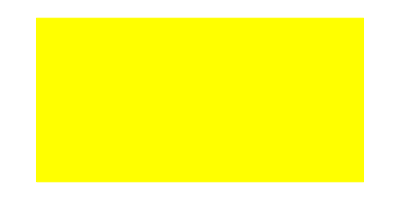
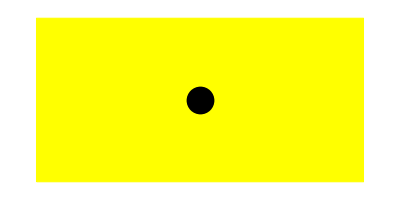
point drawn first: | point drawn second:
-Graphics- | -Graphics-

```mathematica
Module[{p1,p2},
p1=Graphics[{
{PointSize[0.05],Point[{1,0.5}]},
{EdgeForm[Thick],Yellow,Rectangle[{0,0},{2,1}]}
}];
p2=Graphics[{
{EdgeForm[Thick],Yellow,Rectangle[{0,0},{2,1}]},
{PointSize[0.05],Point[{1,0.5}]}
}];
Grid[{{"point drawn first:","point drawn second:"},{Show[p1],Show[p2]}}]
]
```

#### Directives

To apply a Directive to all/one Primitive, enclose both in a set of { }, putting the Directive first. Within this set of { }, if you have several Primitives that, for example, you want to make all different colors while still all sharing one or some same Directives, make sure to pay attention to the order you draw them in:

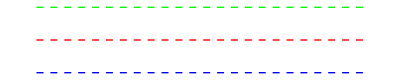

```mathematica
Graphics[{
Thick,Dashed,
Blue,Line[{{0,0},{1,0}}],
Red,Line[{{0,0.1},{1,0.1}}],
Green,Line[{{0,0.2},{1,0.2}}]
}]
```

### Options for Graphics and Plots

#### ImagePadding

ImagePadding prevents a plot from “jiggling”. Often when using Manipulate, as you move the slider, the axes on the plot may change as the function is being evaluated. You’ll see that the values on the vertical axis change and depending on the sig figs, it will look like the numbers are pushing on the plot frame, making the plot “jiggle”. 
Adding ImagePadding basically prevents the plot from expanding/contracting by setting a boundary between the edge of the plot and the bounds of the ImageSize. Think of it like adding a mat board to a picture frame so the picture sits in the frame nice and snug even if the frame is otherwise too big for the picture. Unless you set a PlotRange, you should add ImagePadding before submitting your demonstration.

```mathematica
Plot[f[x],{x,Subscript[x, min],Subscript[x, max]},
ImagePadding->{{left,right},{bottom,top}}]
```

Plot::plln: Limiting value x_min in {x, x_min, x_max} is not a machine-sized real number.

Plot[f[x],{x,x_min,x_max},ImagePadding→{{left,right},{bottom,top}}]

I can’t really explain what the numbers mean, it’s more or less trial-and-error until you find numbers that show all the information on the axes that you need to display. Obviously if there are values and/or labels on the left-axis compared to the right-, you’ll need to put in a larger number. To see the difference ImagePadding makes, use the plot below:

```mathematica
Manipulate[
Plot[Sin[k*x]+1,{x,0,2*π+k*π},
Frame->True,
ImagePadding->If[pad==1,All,{{25,5},{20,5}}]
],
Control[{{pad,1,""},{1->"no padding set",2->"padding set"},Setter}],
Control[{{k,0.25,""},0,0.5}]
]
```

I also use ImagePadding in BarChart or Graphics (see here) if I’m using Graphics to imitate BarChart. For both, I set the minimum (y_min) bound of the PlotRange to zero, but when making a BarChart with Graphics if you do this you won’t be able to see the labels under the bars unless you set ImagePadding (if you lower that y_min the plot will look weird).

### Putting it all together

Here is one that I’ve made before, with comments. Making a graphic isn’t hard; it’s like building something with Legos, just take it piece-by-piece. It’s all on a 2-coordinate system {x,y} for Graphics and a 3-coordinate system {x,y,z} for Graphics3D. You set the range you want to work in, but it might take some trial-and-error to get it right for what you want to make. I usually just start at {0,0} and build from there.

```mathematica
Manipulate[
Module[{Pint,Pext,h1,h2},
Pint=0.1*(1-go)+2*go;
Pext=If[process==1,Pint,2];

h1=0.1+0.8*(1-go);(*how I get the piston/gas/Subscript[P, int]/Subscript[P, ext] to move when you press "play"--see control for "go"*)
h2=h1+0.075;(*how thick piston is/height*)

Graphics[{
{Opacity[0.7,RGBColor[0.16,1.,0.36]],Rectangle[{0,0},{0.7,h1}]},(*light-green gas, Opacity[x,color] is the Directive*)
{EdgeForm[Thick],GrayLevel[0.4],Rectangle[{0,h1},{0.7,h2}]},(*piston, note oprder of the gas and piston, etc.*)
{Thick,(*first Line draws the emply vessel--all lines drawn are Thick*)
Line[{{0,1.12},{0,0},{0.7,0},{0.7,1.12}}],
If[process==2,{(*you can make some elements visible for certaian conditions, here if you select "adiabatic" insulation is shown*)
Line[{{0,1.12},{-0.07,1.12},{-0.07,-0.07},{0.77,-0.07},{0.77,1.12},{0.7,1.12}}],(*outer part of tank*)
(*insulation: instead of writing out each line, you can make a table of the Graphics Primitive. See the next section for an explanation of how I did this*)
Table[Line[{{n*0.07,0},{0.07*(n-1),-0.07}}],{n,0,11}],
Table[{Line[{{-0.07,n*0.07},{0,0.07*(n+1)}}],Line[{{0.7,n*0.07},{0.77,0.07*(n+1)}}]},{n,0,15}]}]
},
(*this looks ugly, Wolfram has rules about how variables, subscripts/superscripts, etc. are written. Also look to the next section for an explanation of this*)
Text[Style[Row[{Subscript[Style["P",Italic],"ext"]," = ",NumberForm[Pext,{3,1}]," MPa"}],18],{0.35,0.27+h1}],
Text[Style[Row[{Style["P",Italic]," = ",NumberForm[Pint,{3,1}]," MPa"}],18],{0.35,0.5*h1}]

},(*all the Options you want to specify for Graphics go here, these options will apply to all Primitives/Directives above*)ImageSize->{400,350},PlotRange->{-0.1,1.25}]
],
Row[{
Control[{{process,1,""},{1->"isothermal",2->"adiabatic"},Setter}],Spacer[30],
Control[{{go,0,""},0,1,Trigger,AnimationRate->1,AppearanceElements->{"PlayPauseButton","ResetButton"}}]
(*initially go=0 and goes to 1 after play is pressed, (initial and final values can be anything this is easier though) I set h1 to change with go; at go=0 h=0.9 and at go=1 h1=0.1 (since rest of expression goes to 0)*)
}]
]
```

### Explanation of elements mentioned in “Putting it all together”

#### Using Tables in Graphics

When you have a lot of repeating elements, you can use Table instead of writing out a bunch of Primitives.

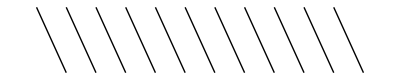

```mathematica
Graphics[Table[Line[{{n,0},{n-1,1}}],{n,0,10}]]
```

#### Displaying data, following Wolfram’s “rule”

You can use Row, Column, and/or Grid to display your data (depending on how you want it to be shown):
	Row → obviously puts everything in a row on the same line,
	Column → stacks each element in a column,
	Grid → combines Row and Column in one function.

If you have text and numerical (or just text sometimes) you need to put it all in one (or more) of the previously mentioned functions to display it. Also in order to submit a Demonstration they want you to style the text a certain way. For example, if you are displaying a variable it needs to be italicized and you can’t use the shortcut (CTRL + i) in your code to achieve this:

please note that I am using Text@ here for demonstration purposes only. I only use Text@ if I want to show data to you or for myself when I’m trying to check to see if my calculations are correct. For the final Demonstration (If I also use Graphics), follow the guidelines for Text in the Documentation Center

```mathematica
Text@Style[
Row[{
Style["P",Italic]," = 2 bar"
}],
16]
```

P = 2 bar

If you’re solving for a variable and want to display it, more decimal points will be displayed than what you probably want shown, so use NumberForm to control the number of displayed digits. This isn’t always necessary if a value is set or if it is a value from a slider. You’ll see though that under “with number formatting” that I used NumberForm on the manipulated variable even though I’ve set the step-size. You can do this to prevent the text from “jiggling.” You can see the “jiggling” on the row with no number formatting as you move the slider.

```mathematica
Manipulate[
Module[{f},
f[x_]=x^2;
Text@Style[
Column[{
"no number formatting:",
Row[{Style["f",Italic],"(",n,") = ",f[n]}],
"with number formatting:",
Row[{Style["f",Italic],"(",NumberForm[n,{3,2}],") = ",NumberForm[f[n],{3,1}]}]
}],16]
],
Control[{{n,2.5,"x"},2,5,0.01}]
]
```

Finally, if you have any subscripts/superscripts you need to use the following functions in the code instead of using the shortcuts (CTRL + 6 or CTRL + -):
	x_1 → Subscript[“x”,1]
	x^L → Superscript[“x”,”L”]
	x_1^L → Subsuperscript[“x”,1,“L”]
If “x” is a variable, italicize it:
	Subscript[Style[“x”,Italic], 1]

Putting it all together:

```mathematica
Manipulate[
Module[{Psat},
Psat=10^(3.98292-819.296/(T+248.6));
Text@Style[
Column[{
Row[{Style["T",Italic]," = ",T," °C"}],
Row[{Superscript[Style["P",Italic],"sat"]," = ",NumberForm[Psat,{3,1}]," bar"}]
},Alignment->"="],
16]
],
Control[{{T,35,"temperature (°C)"},25,45,1}]
]
```

### Mistakes I’ve seen

#### Putting each Primitive inside a new Graphics

If you’re making a Graphics object with more than one Primitive, they can all go inside the same Graphics unless, obviously, they should not be shown together (different Graphics should be shown for different conditions).

DON'T DO:

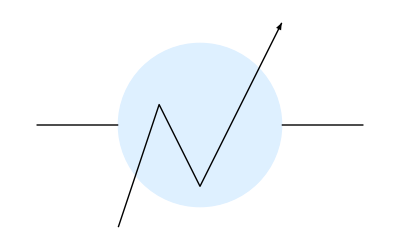

```mathematica
Show[
Graphics[{EdgeForm[Thick],LightBlue,Disk[]}],
Graphics[{Thick,Line[{{-2,0},{-1,0}}]}],
Graphics[{Thick,Line[{{1,0},{2,0}}]}],
Graphics[{Thick,Arrow[{{-1,-1.25},{-0.5,0.25},{0,-0.75},{1,1.25}}]}]
]
```

DO:
Put it all in one Graphics and use curly brackets. Also, if you are using the same Directive, like Thick, on more than one Directive, they can all be included inside the same set of { }. Notice that there is one set of { } overall and then additional sets wrapped around Directives and Primitives.

```mathematica
Graphics[{
{EdgeForm[Thick],LightBlue,Disk[]},
{Thick,Line[{{-2,0},{-1,0}}],Line[{{1,0},{2,0}}],
Arrow[{{-1,-1.25},{-0.5,0.25},{0,-0.75},{1,1.25}}]}
}]
```

-Graphics-

### Controlling which Graphics are displayed using Controls

You can use Switch and/or If or Which to show some Plots or Graphics for certain conditions. For just a few elements in Graphics that you only want displayed at certain conditions, use If or Which. If you want to switch out entire Graphics or Plots with a button, use Switch.

#### Using Switch to show different graphs

```mathematica
Manipulate[
Module[{p1,p2},
p1=Plot[Sin[x],{x,0,2*π},PlotStyle->{Thick,Blue}];
p2=Plot[Cos[x],{x,0,2*π},PlotStyle->{Thick,Purple}];
Show[Switch[cs,1,p1,2,p2],Frame->True]
],
Control[{{cs,1,""},{1->" Sin(x) ",2->" Cos(x) "},Setter}]
]
```

#### Using If to display labels

```mathematica
Manipulate[
Show[
Plot[{Sin[x],Cos[x]},{x,0,2*π},PlotStyle->{{Thick,Blue},{Thick,Purple}},Frame->True,Axes->False,PlotRange->{-1.15,1.25}],
Graphics[{
If[TrueQ[label],{
Text[Style["Sin(x)",16,Background->White],{π/2,Sin[π/2]}],
Text[Style["Cos(x)",16,Background->White],{π/2,Cos[π/2]}]
}],
{PointSize[0.0275],Point[{pt,Sin[pt]}],Point[{pt,Cos[pt]}]}
}]
],
Control[{{label,True,"show labels"},{True,False}}],
Control[{{pt,π,"point"},0,2*π}]
]
```

### Using Set (=) and SetDelayed (:=)

Wolfram would like us to used SetDelayed in our Demonstrations instead of Set, when appropriate. With SetDelayed, the function is not evaluated until it is called on as opposed to Set where the function is evaluated every time the code is evaluated. Wolfram has a nice explanation of the two here.

```mathematica
Manipulate[
Module[{k,vo,τ,Ca},
k=0.1;
vo=10;

τ:=V/vo;
Ca:=Ca0/(1+k*τ);

Plot[Ca,{V,0,200}]
],
Control[{{Ca0,1,"C_(A, 0)"},Range[5],Setter}]
]
```